# Sedimentary Clast Shape Parameters Analysis

This notebook is the code Presented in “Image Analysis for Quantifying 2D Particle Shape Parameters using Mathematica”.

## Set Directory

```mathematica
(*Specify Directory where image files are located *)
SetDirectory["C:\\Users\\Dave\\Documents\\sed parameters"];
```

## Import File

```mathematica
inputimage=rawimage=Import["ggc1.bmp"]
(* Check raw image file *)
```

-Graphics-

## Image Preparataion

If the image is not a Grain Boundary Map and is a simple image where grain boundaries can be accurately identified, then the following code can be used to create Grain Boundary Maps, otherwise skip this step.

```mathematica
rawimage//ColorNegate//DeleteSmallComponents//ColorNegate;
Dilation[EdgeDetect[%],-2]//ColorNegate;
SelectComponents[%,"EnclosingComponentCount",#==0&];
inputimage=Dilation[EdgeDetect[%],-.5]//ColorNegate
```

-Graphics-

## Grain Detection

Identifies grains and identifies them with labels and best fit circles

```mathematica
grains=SelectComponents[inputimage,"Count",1000<#<100000&]; 
(*This line sets the size of the objects identified, if unwanted small objects are being identified, increase the 1st value, likewise if oversized objects are being identified lower the 2nd value*)
grainsdata=ComponentMeasurements[grains,{"EquivalentDiskRadius","Centroid","Length","Width","Orientation","Label"}];
Show[inputimage,Table[Graphics[
{Blue,GeometricTransformation[Circle[grainsdata[[i,2,2]],
{grainsdata[[i,2,3]],grainsdata[[i,2,4]]}/2],RotationTransform[grainsdata[[i,2,5]],grainsdata[[i,2,2]]]],{Blue,Text[Style[grainsdata[[i,2,6]],Medium],grainsdata[[i,2,2]]]}}],{i,1,Length[grainsdata]}],ImageSize->Scaled[1]]
```

-Graphics-

## Area Calculations in mm and pixels

Grain area in mm

This stage converts the image dimensions from pixels to millimetres. If scale is not an issue than this stage can be skipped.

30 Total Objects

Object Lengths in mm

{9.13531,8.83785,9.36849,9.99561,10.3284,9.07794,8.98717,8.47535,9.53136,9.34136,9.23451,9.19154,8.67082,11.4537,9.57149,9.93818,9.78421,8.25995,9.83276,9.1065,10.4114,8.44543,9.38307,7.96053,11.562,9.47697,8.15463,10.1925,8.58706,9.67591}

Object Widths in mm

{7.9411,7.33284,7.73794,7.53815,6.86754,7.4108,7.16951,8.16582,7.01071,7.36128,7.62231,7.89907,8.023,8.22157,8.90704,7.6034,6.42682,7.29344,7.67308,7.54991,7.90991,7.0919,8.76837,7.37403,7.11939,7.92439,7.82855,7.78539,7.41487,8.34732}

Object Areas in mm^2

{55.5767,50.6047,56.9452,58.3511,54.3471,49.9689,50.1344,50.7386,51.9529,52.521,54.1226,56.396,53.655,73.5235,66.333,59.0302,47.6909,46.3378,57.8993,52.6202,64.6475,46.6381,64.5619,46.0127,63.3192,57.0918,49.7745,60.3834,49.8386,62.8471}

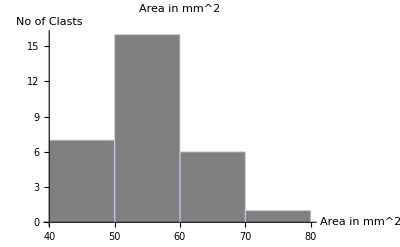

```mathematica
(* This set of code converts the image dimensions from pixels to microns and requires the user to place the image width in mm in the first line*)

imagewidth= 100; (* give actual width of image in mm, ie. 2 or 2000mm *)
pixelwidth=Part[ImageDimensions[inputimage],1];
 f = (imagewidth)/(pixelwidth);
ComponentMeasurements[grains, "LabelCount"];
%/.Rule->List;
Mean[Last/@% ]"Total Objects"
"Object Lengths in mm"  
l=ComponentMeasurements[grains, "Length"]/.Rule->List;  
lengthmm=Last/@l*f
"Object Widths in mm"
w=ComponentMeasurements[grains, "Width"]/.Rule->List;
widthmm=Last/@w*f
a=ComponentMeasurements[grains, "Area"]/.Rule->List;
"Object Areas in mm^2"
sizedatamm=areamm=Last/@a*f^2
Histogram[sizedatamm, AxesLabel->{"Area in mm^2","No of Clasts"},PlotLabel->Style["Area in mm^2" ,"Label",14 ,Bold], ChartStyle->{Gray}]
```

Grain Size Distribution (mm)

```mathematica
qmm=Flatten[Quartiles[sizedatamm]]; 
q1mm=Take[qmm,{1}]; q2mm=Take[qmm,{2}]; q3mm=Take[qmm,{3}]; mediangrainsize=q2mm; sortingcoefficient= √(q3mm/q1mm); skewness=(q1mm×q3mm)/q2mm^2; Grid[{{Quartiles,Q1,Q2,Q3},{,q1mm,q2mm,q3mm}}, ItemSize->9
,Frame->All] Grid[{{"Median Grain Size",q2mm},{"Sorting Coefficient",sortingcoefficient}, {"Skewness",skewness}}, ItemSize->9
,Frame->All]
```

Quartiles | Q1 | Q2 | Q3
 | {50.1344} | {54.2349} | {59.0302} Median Grain Size | {54.2349}
Sorting Coefficient | {1.0851}
Skewness | {1.00613}

Grain area in pixels

Length in pixels

{152.103,147.15,155.985,166.427,171.968,151.148,149.636,141.115,158.697,155.534,153.755,153.039,144.369,190.704,159.365,165.471,162.907,137.528,163.715,151.623,173.351,140.616,156.228,132.543,192.507,157.792,135.775,169.705,142.975,161.104}

Width in pixels

{132.219,122.092,128.837,125.51,114.345,123.39,119.372,135.961,116.728,122.565,126.911,131.52,133.583,136.889,148.302,126.597,107.006,121.436,127.757,125.706,131.7,118.08,145.993,122.778,118.538,131.941,130.345,129.627,123.458,138.983}

Area in pixels

{15407.1,14028.8,15786.5,16176.3,15066.3,13852.5,13898.4,14065.9,14402.5,14560.,15004.,15634.3,14874.4,20382.4,18389.,16364.5,13221.,12845.9,16051.,14587.5,17921.8,12929.1,17898.,12755.8,17553.5,15827.1,13798.6,16739.6,13816.4,17422.6}

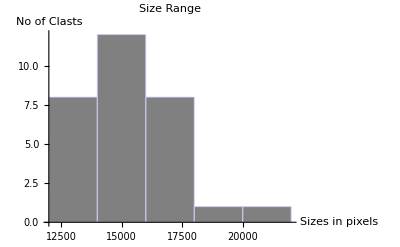

```mathematica
"Length in pixels"  
lp=ComponentMeasurements[grains, "Length"]/.Rule->List;
lengthp=Last/@lp
"Width in pixels"
wp=ComponentMeasurements[grains, "Width"]/.Rule->List;
widthp=Last/@wp
"Area in pixels"
ap=ComponentMeasurements[grains, "Area"]/.Rule->List;
sizedatap=areap=Last/@%
Histogram[sizedatap, AxesLabel->{"Sizes in pixels","No of Clasts"},PlotLabel->Style["Size Range" ,"Label",14 ,Bold], ChartStyle->{Gray}]
ComponentMeasurements[grains, "LabelCount"];
%/.Rule->List;
Mean[Last/@% ]"Total";
```

Grain Size Distribution (pixels)

```mathematica
qp=Flatten[Quartiles[sizedatap]]; q1p=Take[qp,{1}]; q2p=Take[qp,{2}]; q3p=Take[qp,{3}];
mediangrainsize=q2p; sortingcoefficient= √(q3p/q1p); skewness=(q1p×q3p)/q2p^2; Grid[{{Quartiles,Q1,Q2,Q3},{,q1p,q2p,q3p}}, ItemSize->9
,Frame->All] Grid[{{"Median Grain Size",q2p},{"Sorting Coefficient",sortingcoefficient}, {"Skewness",skewness}}, ItemSize->9
,Frame->All]
```

Quartiles | Q1 | Q2 | Q3
 | {13898.4} | {15035.1} | {16364.5} Median Grain Size | {15035.1}
Sorting Coefficient | {1.0851}
Skewness | {1.00613}

## Fractal Dimension

1.31762
1.31385
1.31788
1.30883
1.32068
1.32259
1.32137
1.32872
1.32249
1.32756
1.30701
1.31778
1.32461
1.31163
1.296
1.32197
1.32987
1.32846
1.32461
1.31849
1.30836
1.32676
1.30988
1.31726
1.31315
1.32381
1.31771
1.32023
1.31595
1.32204

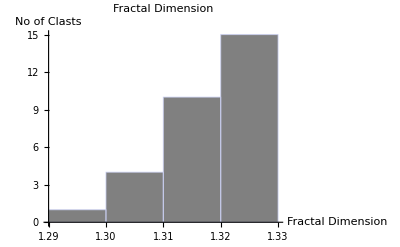

```mathematica
ComponentMeasurements[grains, "Area"]/.Rule->List;
a=Last/@%;
ComponentMeasurements[grains, "PerimeterLength"]/.Rule->List;
p=Last/@%;
fddata=2{{Log[p]}/{Log[a]}}//Flatten;
TableForm[%]
Histogram[fddata, AxesLabel->{"Fractal Dimension","No of Clasts"},PlotLabel->Style["Fractal Dimension" ,"Label",14 ,Bold], ChartStyle->{Gray}]
```

```mathematica
lengthp=Last/@lp
"Width in pixels"
wp=ComponentMeasurements[grains, "Width"]/.Rule->List;
widthp=Last/@wp
"Area in pixels"
ap=ComponentMeasurements[grains, "Area"]/.Rule->List;
sizedatap=areap=Last/@%
Histogram[sizedatap, AxesLabel->{"Sizes in pixels","No of Clasts"},PlotLabel->Style["Size Range" ,"Label",14 ,Bold], ChartStyle->{Gray}]
ComponentMeasurements[grains, "LabelCount"];
%/.Rule->List;
Mean[Last/@% ]"Total";
```

## Shape Parameters

Sphericity/Roundness

Sphericity Calculations (Wadell, 1932)

All Clasts

0.886991
0.871097
0.893925
0.835774
0.781791
0.775729
0.875536
0.84866
0.813708
0.856262
0.861582
0.879641
0.877109
0.840819
0.909166
0.844909
0.790003
0.885245
0.825656
0.870601
0.85583
0.913939
0.935726
0.941424
0.768481
0.8345
0.929624
0.817968
0.919886
0.867519

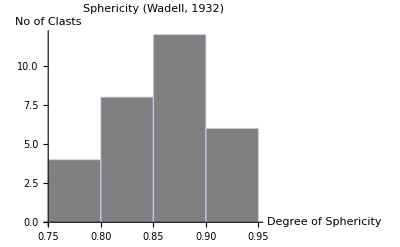

```mathematica
"Sphericity Calculations (Wadell, 1932)"
ComponentMeasurements[grains, "EquivalentDiskRadius"];
%/.Rule->List;
da=(Last/@%)*2  (*Diameter of a circle with the same area as particle*);
ComponentMeasurements[grains, "BoundingDiskRadius"];
%/.Rule->List;
dc=(Last/@%)*2 (*Diameter of the smallest circumscribed circle*);
wadellsphericitydata=data =(da/dc);

r2=Mean[%] ;
"Min";
Min[data];
"Max";
Max[data];
"All Clasts"
TableForm[data]
l2="Mean Sphericity";
Histogram[data, AxesLabel->{"Degree of Sphericity","No of Clasts"},PlotLabel->Style["Sphericity (Wadell, 1932)" ,"Label",14, Bold], ChartStyle->{Gray}]
```

Circularity

Degree of Circularity Calculations (Wadell, 1932)

All Clasts

0.766574
0.792207
0.762667
0.793772
0.758046
0.761357
0.76541
0.737587
0.756985
0.737493
0.810109
0.764215
0.745412
0.755366
0.828812
0.743407
0.741096
0.749587
0.736251
0.770053
0.78311
0.754828
0.777459
0.791239
0.767424
0.740814
0.779797
0.746981
0.786187
0.735707

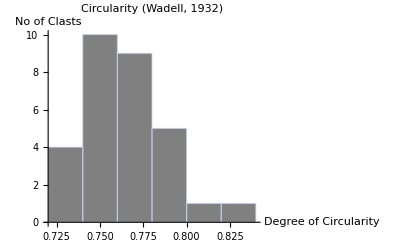

```mathematica
"Degree of Circularity Calculations (Wadell, 1932)"
ComponentMeasurements[grains, "Area"];
%/.Rule->List;
pa=(2*(√((Last/@%)/(Pi) )))*(Pi)(*Perimeter of a circle with the same area as particle*);
ComponentMeasurements[grains, "PerimeterLength"];
%/.Rule->List;
pp=Last/@% (*Perimeter of Clast*);
wadellcircularitydata=data=pa/pp;
r3=Mean[%] ;
"Min";
Min[data];
"Max";
Max[data];
"All Clasts"
TableForm[data]
l3="Degree of Circularity";
Histogram[data, AxesLabel->{"Degree of Circularity","No of Clasts"},PlotLabel->Style["Circularity (Wadell, 1932)" ,"Label",14, Bold], ChartStyle->{Gray}]
```

Roundness

Roundness Calculations (Tickell and Hiatt, 1938)

All Clasts

0.789168
0.761347
0.801818
0.700738
0.613324
0.604088
0.769129
0.722477
0.664776
0.735915
0.744955
0.776662
0.771362
0.709181
0.829289
0.716257
0.626759
0.786406
0.684266
0.760892
0.734813
0.838146
0.878184
0.88933
0.592268
0.699046
0.867636
0.6709
0.848918
0.755043

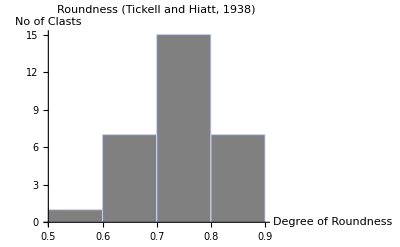

```mathematica
"Roundness Calculations (Tickell and Hiatt, 1938)"
"Mean";
ComponentMeasurements[grains, "Area"];
%/.Rule->List;
ap=Last/@%  (*Area of Clast*);
ComponentMeasurements[grains, "BoundingDiskRadius"];
%/.Rule->List;
ac=(Pi)*(Last/@%^2);(*Area of the Smallest Circumscribed Circle*);
roundnessdata= data=ap/ac;
r5=Mean[%] ;
"Min";
Min[data];
"Max";
Max[data];
"All Clasts"
TableForm[data]
l5="Mean Roundness";
Histogram[data, AxesLabel->{"Degree of Roundness","No of Clasts"},PlotLabel->Style["Roundness (Tickell and Hiatt, 1938)" ,"Label",14, Bold], ChartStyle->{Gray}]
```

Angularity

Angularity Calculations

Mean

All Clasts

0.847924
0.824912
0.826092
0.743602
0.648666
0.772031
0.790314
0.899358
0.728132
0.766342
0.808093
0.849928
0.908658
0.713582
0.921894
0.760976
0.6343
0.864749
0.762488
0.807904
0.759347
0.832543
0.933676
0.924494
0.603089
0.809366
0.953034
0.740062
0.860571
0.854695

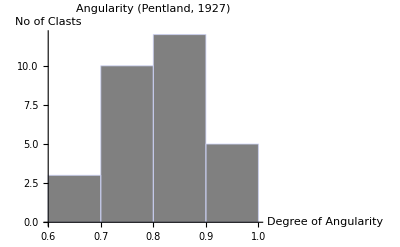

```mathematica
"Angularity Calculations" (*a perfect circle should give a value of 1, values trending towards zero refrer to an increase in angularity (Pentland, 1927)*)
"Mean"
ComponentMeasurements[grains, "Area"];
%/.Rule->List;
ap=Last/@%  (*Area of Clast*);
ComponentMeasurements[grains, "Length"];
%/.Rule->List;
ac2=((Last/@%)/(2))^2*(Pi) (*Area of a Circle with a Diameter equal to the longest distance between two points*);
angularitydata=data=ap/ac2;
r6=Mean[%] ;
"Min";
Min[data];
"Max";
Max[data];
"All Clasts"
TableForm[data]
l6="Mean Roundness";
Histogram[data, AxesLabel->{"Degree of Angularity","No of Clasts"},
PlotLabel->Style["Angularity (Pentland, 1927)" ,"Label",14, Bold], ChartStyle->{Gray}]
```

Roundness/Circularity

Roundness/Circularity Calculations (Riley, 1941)

All Clasts

0.587635
0.627592
0.581661
0.630073
0.574634
0.579665
0.585853
0.544035
0.573027
0.543895
0.656277
0.584024
0.555639
0.570578
0.686929
0.552654
0.549223
0.561881
0.542066
0.592982
0.613261
0.569766
0.604442
0.626058
0.58894
0.548806
0.608083
0.55798
0.618091
0.541264

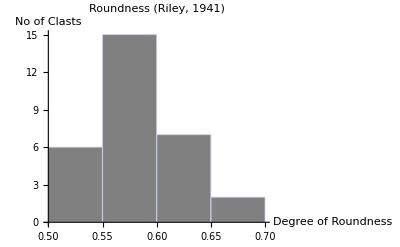

```mathematica
"Roundness/Circularity Calculations (Riley, 1941)"
"Mean";
ComponentMeasurements[grains, "Area"];
%/.Rule->List;
ap=Last/@%  (*Area of Clast*);
ComponentMeasurements[grains, "PerimeterLength"];
%/.Rule->List;
pp=Last/@% (*Perimeter of Clast*);
rileyroundnessdata= data=((4*Pi)*(ap))/(pp^2);
r7=Mean[%] ;
"Min";
Min[data];
"Max";
Max[data];
"All Clasts"
TableForm[data]
l7="Mean Roundness";
Histogram[data, AxesLabel->{"Degree of Roundness","No of Clasts"},
PlotLabel->Style["Roundness (Riley, 1941)" ,"Label",14, Bold], ChartStyle->{Gray}]
```

Roughness

Convexity

All Clasts

0.80661
0.817874
0.782382
0.841617
0.819427
0.835361
0.791192
0.800242
0.799058
0.779724
0.855018
0.796617
0.779105
0.793453
0.858807
0.775823
0.808816
0.781316
0.780605
0.81861
0.808811
0.781424
0.791066
0.807723
0.830246
0.793333
0.806509
0.801086
0.805657
0.764674

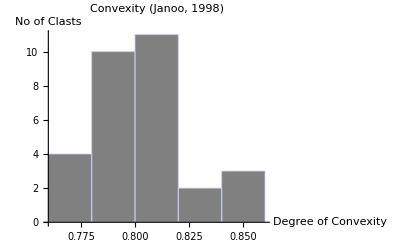

```mathematica
"Convexity"
(*measure of shape irregularity; values tending towards 1 represents a regular shape, while values tending towards 0 represent increases in irregularity (Janoo, 1998)*)
ComponentMeasurements[grains, "PerimeterLength"];
%/.Rule->List;
pp=Last/@% (*Perimeter of Clast*);
ComponentMeasurements[grains, "ConvexPerimeterLength"];
%/.Rule->List;
cp=Last/@% (*Convex Perimeter of Clast*);
convexitydata=data=cp/pp;
r8=Mean[%] ;
"Min";
Min[data];
"Max";
Max[data];
"All Clasts"
TableForm[data]
l8="Mean Convexity";
Histogram[data, AxesLabel->{"Degree of Convexity","No of Clasts"},PlotLabel->Style["Convexity (Janoo, 1998)" ,"Label",14, Bold], ChartStyle->{Gray}]
```

Caliper Elongation

Caliper Elongation

All Clasts

0.100508
0.220285
0.185547
0.276566
0.347271
0.224657
0.208922
0.0946954
0.290713
0.216446
0.200211
0.171709
0.130674
0.267774
0.18529
0.231308
0.297681
0.125183
0.23282
0.181542
0.245765
0.160796
0.0906576
0.0955665
0.378894
0.141442
0.103836
0.240545
0.152202
0.203091

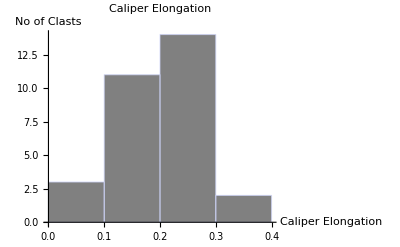

```mathematica
"Caliper Elongation"
(*Calculated as 1–(caliper width/caliper length), where the caliper length is the largest diameter of the convex hull and the caliper width is the smallest diameter of the convex hull. This function essentially describes shape or form without reference to surface textures*) 
ComponentMeasurements[grains, "CaliperElongation"];
%/.Rule->List;
caliperelongationdata=data=Last/@% ;
r8a=Mean[%] ;
"Min";
Min[data];
"Max";
Max[data];
"All Clasts"
TableForm[data]
l8a="Mean Caliper Elongation";
Histogram[data, AxesLabel->{"Caliper Elongation","No of Clasts"},PlotLabel->Style["Caliper Elongation" ,"Label",14, Bold], ChartStyle->{Gray}]
```

Shape Parameter Summary Table

```mathematica
Grid[{{l2,l3,l5,l6,l7,l8,l8a},{r2,r3,r5,r6,r7,r8, r8a}}, ItemSize->7.3
,Frame->All]
```

Mean Sphericity | Degree of Circularity | Mean Roundness | Mean Roundness | Mean Roundness | Mean Convexity | Mean Caliper Elongation
0.860303 | 0.764665 | 0.74477 | 0.805027 | 0.585234 | 0.80374 | 0.200087

## Elongation, Aspect Ratio and Eccentricity

Elongation

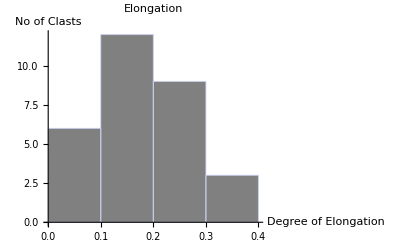

```mathematica
(*Mean Elongation 1-width/length; closer to 0 perfect sphere, closer to 1 highly elongate*)
ComponentMeasurements[grains, "Elongation"];
%/.Rule->List;
elongationdata =data=Last/@%;
r9=Mean[%];
l9="Mean Elongation";
Histogram[data, AxesLabel->{"Degree of Elongation","No of Clasts"},
PlotLabel->Style["Elongation" ,"Label",14, Bold], ChartStyle->{Gray}]
```

Aspect Ratio

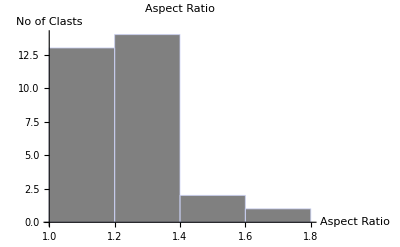

```mathematica
(*Aspect Ratio*)
ComponentMeasurements[grains, "Length"];
%/.Rule->List;
l=Last/@%;
ComponentMeasurements[grains, "Width"];
%/.Rule->List;
w=Last/@%;
aspectdata=data=l/w;
r10=Mean[%];
l10="Aspect Ratio";
Histogram[data, AxesLabel->{"Aspect Ratio","No of Clasts"},PlotLabel->Style["Aspect Ratio" ,"Label",14, Bold], ChartStyle->{Gray}]
```

Eccentricity

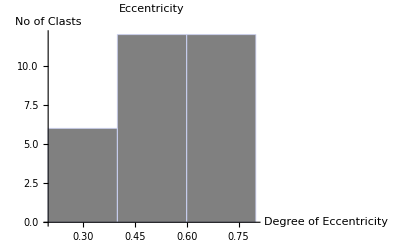

```mathematica
(*Eccentricity => The eccentricity of a circle is zero.The eccentricity of an ellipse which is not a circle is greater than zero but less than 1. The eccentricity of a parabola is 1. The eccentricity of a hyperbola is greater than 1.*)
ComponentMeasurements[grains, "Eccentricity"];
%/.Rule->List;
eccentricitydata=data=Last/@%;
r11=Mean[%];
l11="Eccentricity";
Histogram[data, AxesLabel->{"Degree of Eccentricity","No of Clasts"},
PlotLabel->Style["Eccentricity" ,"Label",14, Bold], ChartStyle->{Gray}]
```

Elongation, Aspect Ratio and Eccentricity Summary Table

```mathematica
Grid[{{l9,l10,l11},{r9,r10,r11}}, ItemSize->7.3
,Frame->All]
```

Mean Elongation | Aspect Ratio | Eccentricity
0.180659 | 1.23531 | 0.550948

## Overall Summary Table

```mathematica
Grid[{{l2,l3,l5,l6,l7,l8,l8a,l9,l10,l11},{r2,r3, r5,r6,r7,r8,r8a,r9,r10,r11}}, ItemSize->9
,Frame->All]
```

Mean Sphericity | Degree of Circularity | Mean Roundness | Mean Roundness | Mean Roundness | Mean Convexity | Mean Caliper Elongation | Mean Elongation | Aspect Ratio | Eccentricity
0.860303 | 0.764665 | 0.74477 | 0.805027 | 0.585234 | 0.80374 | 0.200087 | 0.180659 | 1.23531 | 0.550948

## Export to Excel

```mathematica
areainmm=Join[{"Area in MM"},{areamm}]//Flatten;  lengthinmm=Join[{"Length in MM"},{lengthmm}]//Flatten; widthinmm=Join[{"Width in MM"},{widthmm}]//Flatten; areainp= Join[{"Area in Pixels"},{areap}]//Flatten; lengthinp=Join[{"Length in Pixels"},{lengthp}]//Flatten; widthinp= Join[{"Width in Pixels"},{widthp}]//Flatten;
fddataout=Join[{"Fractal Dimension"}, {fddata}]//Flatten;
wadellsphericitydataout=Join[{"Wadell 1932 Sphericity"},{wadellsphericitydata}]//Flatten;wadellcircularitydataout=Join[{"Wadell 1932 Circularity"},{wadellcircularitydata}]//Flatten; roundnessdataout=Join[{"Tickell & Hiatt 1938 roundness"},{roundnessdata}]//Flatten; roundnessrileyout=Join[{"Riley 1941 roundness"},{rileyroundnessdata}]//Flatten; angularitydataout=Join[{"Pentland 1927 Angularity"},{angularitydata}]//Flatten; convexitydataout=Join[{"Janoo 1998 Convexity"},{convexitydata}]//Flatten; caliperelongationdataout=Join[{"Caliper Elongation"},{caliperelongationdata}]//Flatten; elongationdataout=Join[{"Elongation"},{elongationdata}]//Flatten; aspectdataout=Join[{"Aspect Ratio"},{aspectdata}]//Flatten; eccentricitydataout=Join[{"Eccentricity"},{eccentricitydata}]//Flatten;
alldata=Table[{areainmm,lengthinmm,widthinmm, areainp, lengthinp, widthinp,fddataout,wadellsphericitydataout, wadellcircularitydataout, roundnessdataout ,roundnessrileyout,angularitydataout, convexitydataout,caliperelongationdataout,elongationdataout,aspectdataout, eccentricitydataout}]//Transpose//TableForm
```

Area in MM | Length in MM | Width in MM | Area in Pixels | Length in Pixels | Width in Pixels | Fractal Dimension | Wadell 1932 Sphericity | Wadell 1932 Circularity | Tickell & Hiatt 1938 roundness | Riley 1941 roundness | Pentland 1927 Angularity | Janoo 1998 Convexity | Caliper Elongation | Elongation | Aspect Ratio | Eccentricity
55.5767 | 9.13531 | 7.9411 | 15407.1 | 152.103 | 132.219 | 1.31762 | 0.886991 | 0.766574 | 0.789168 | 0.587635 | 0.847924 | 0.80661 | 0.100508 | 0.130724 | 1.15038 | 0.494327
50.6047 | 8.83785 | 7.33284 | 14028.8 | 147.15 | 122.092 | 1.31385 | 0.871097 | 0.792207 | 0.761347 | 0.627592 | 0.824912 | 0.817874 | 0.220285 | 0.170291 | 1.20524 | 0.558196
56.9452 | 9.36849 | 7.73794 | 15786.5 | 155.985 | 128.837 | 1.31788 | 0.893925 | 0.762667 | 0.801818 | 0.581661 | 0.826092 | 0.782382 | 0.185547 | 0.174046 | 1.21072 | 0.563737
58.3511 | 9.99561 | 7.53815 | 16176.3 | 166.427 | 125.51 | 1.30883 | 0.835774 | 0.793772 | 0.700738 | 0.630073 | 0.743602 | 0.841617 | 0.276566 | 0.245854 | 1.326 | 0.656706
54.3471 | 10.3284 | 6.86754 | 15066.3 | 171.968 | 114.345 | 1.32068 | 0.781791 | 0.758046 | 0.613324 | 0.574634 | 0.648666 | 0.819427 | 0.347271 | 0.335081 | 1.50394 | 0.746916
49.9689 | 9.07794 | 7.4108 | 13852.5 | 151.148 | 123.39 | 1.32259 | 0.775729 | 0.761357 | 0.604088 | 0.579665 | 0.772031 | 0.835361 | 0.224657 | 0.183648 | 1.22496 | 0.577554
50.1344 | 8.98717 | 7.16951 | 13898.4 | 149.636 | 119.372 | 1.32137 | 0.875536 | 0.76541 | 0.769129 | 0.585853 | 0.790314 | 0.791192 | 0.208922 | 0.202251 | 1.25353 | 0.602989
50.7386 | 8.47535 | 8.16582 | 14065.9 | 141.115 | 135.961 | 1.32872 | 0.84866 | 0.737587 | 0.722477 | 0.544035 | 0.899358 | 0.800242 | 0.0946954 | 0.0365213 | 1.03791 | 0.267785
51.9529 | 9.53136 | 7.01071 | 14402.5 | 158.697 | 116.728 | 1.32249 | 0.813708 | 0.756985 | 0.664776 | 0.573027 | 0.728132 | 0.799058 | 0.290713 | 0.264458 | 1.35954 | 0.677479
52.521 | 9.34136 | 7.36128 | 14560. | 155.534 | 122.565 | 1.32756 | 0.856262 | 0.737493 | 0.735915 | 0.543895 | 0.766342 | 0.779724 | 0.216446 | 0.211969 | 1.26899 | 0.615635
54.1226 | 9.23451 | 7.62231 | 15004. | 153.755 | 126.911 | 1.30701 | 0.861582 | 0.810109 | 0.744955 | 0.656277 | 0.808093 | 0.855018 | 0.200211 | 0.174584 | 1.21151 | 0.564525
56.396 | 9.19154 | 7.89907 | 15634.3 | 153.039 | 131.52 | 1.31778 | 0.879641 | 0.764215 | 0.776662 | 0.584024 | 0.849928 | 0.796617 | 0.171709 | 0.140615 | 1.16362 | 0.511329
53.655 | 8.67082 | 8.023 | 14874.4 | 144.369 | 133.583 | 1.32461 | 0.877109 | 0.745412 | 0.771362 | 0.555639 | 0.908658 | 0.779105 | 0.130674 | 0.0747127 | 1.08075 | 0.379267
73.5235 | 11.4537 | 8.22157 | 20382.4 | 190.704 | 136.889 | 1.31163 | 0.840819 | 0.755366 | 0.709181 | 0.570578 | 0.713582 | 0.793453 | 0.267774 | 0.282191 | 1.39313 | 0.69624
66.333 | 9.57149 | 8.90704 | 18389. | 159.365 | 148.302 | 1.296 | 0.909166 | 0.828812 | 0.829289 | 0.686929 | 0.921894 | 0.858807 | 0.18529 | 0.0694195 | 1.0746 | 0.366087
59.0302 | 9.93818 | 7.6034 | 16364.5 | 165.471 | 126.597 | 1.32197 | 0.844909 | 0.743407 | 0.716257 | 0.552654 | 0.760976 | 0.775823 | 0.231308 | 0.23493 | 1.30707 | 0.643947
47.6909 | 9.78421 | 6.42682 | 13221. | 162.907 | 107.006 | 1.32987 | 0.790003 | 0.741096 | 0.626759 | 0.549223 | 0.6343 | 0.808816 | 0.297681 | 0.343144 | 1.5224 | 0.754016
46.3378 | 8.25995 | 7.29344 | 12845.9 | 137.528 | 121.436 | 1.32846 | 0.885245 | 0.749587 | 0.786406 | 0.561881 | 0.864749 | 0.781316 | 0.125183 | 0.117012 | 1.13252 | 0.469395
57.8993 | 9.83276 | 7.67308 | 16051. | 163.715 | 127.757 | 1.32461 | 0.825656 | 0.736251 | 0.684266 | 0.542066 | 0.762488 | 0.780605 | 0.23282 | 0.219641 | 1.28146 | 0.625332
52.6202 | 9.1065 | 7.54991 | 14587.5 | 151.623 | 125.706 | 1.31849 | 0.870601 | 0.770053 | 0.760892 | 0.592982 | 0.807904 | 0.81861 | 0.181542 | 0.170932 | 1.20617 | 0.559147
64.6475 | 10.4114 | 7.90991 | 17921.8 | 173.351 | 131.7 | 1.30836 | 0.85583 | 0.78311 | 0.734813 | 0.613261 | 0.759347 | 0.808811 | 0.245765 | 0.240268 | 1.31625 | 0.650236
46.6381 | 8.44543 | 7.0919 | 12929.1 | 140.616 | 118.08 | 1.32676 | 0.913939 | 0.754828 | 0.838146 | 0.569766 | 0.832543 | 0.781424 | 0.160796 | 0.160268 | 1.19086 | 0.543001
64.5619 | 9.38307 | 8.76837 | 17898. | 156.228 | 145.993 | 1.30988 | 0.935726 | 0.777459 | 0.878184 | 0.604442 | 0.933676 | 0.791066 | 0.0906576 | 0.0655114 | 1.0701 | 0.355993
46.0127 | 7.96053 | 7.37403 | 12755.8 | 132.543 | 122.778 | 1.31726 | 0.941424 | 0.791239 | 0.88933 | 0.626058 | 0.924494 | 0.807723 | 0.0955665 | 0.0736759 | 1.07954 | 0.376728
63.3192 | 11.562 | 7.11939 | 17553.5 | 192.507 | 118.538 | 1.31315 | 0.768481 | 0.767424 | 0.592268 | 0.58894 | 0.603089 | 0.830246 | 0.378894 | 0.384241 | 1.62401 | 0.787935
57.0918 | 9.47697 | 7.92439 | 15827.1 | 157.792 | 131.941 | 1.32381 | 0.8345 | 0.740814 | 0.699046 | 0.548806 | 0.809366 | 0.793333 | 0.141442 | 0.163826 | 1.19592 | 0.548464
49.7745 | 8.15463 | 7.82855 | 13798.6 | 135.775 | 130.345 | 1.31771 | 0.929624 | 0.779797 | 0.867636 | 0.608083 | 0.953034 | 0.806509 | 0.103836 | 0.039988 | 1.04165 | 0.279959
60.3834 | 10.1925 | 7.78539 | 16739.6 | 169.705 | 129.627 | 1.32023 | 0.817968 | 0.746981 | 0.6709 | 0.55798 | 0.740062 | 0.801086 | 0.240545 | 0.236163 | 1.30918 | 0.64541
49.8386 | 8.58706 | 7.41487 | 13816.4 | 142.975 | 123.458 | 1.31595 | 0.919886 | 0.786187 | 0.848918 | 0.618091 | 0.860571 | 0.805657 | 0.152202 | 0.136507 | 1.15809 | 0.504361
62.8471 | 9.67591 | 8.34732 | 17422.6 | 161.104 | 138.983 | 1.32204 | 0.867519 | 0.735707 | 0.755043 | 0.541264 | 0.854695 | 0.764674 | 0.203091 | 0.137309 | 1.15916 | 0.505732

```mathematica
Export["data.xls",alldata];
SystemOpen["data.xls"]
```